First we set the phases to zero in the vacuum conditions

```mathematica
LH1M=Higgs1Mod/.{phi2->0,phiS->0};
LH2M=Higgs2Mod/.{phi2->0,phiS->0};
LH2P=Higgs2Phase/.{phi2->0,phiS->0};
LSM=SingletMod/.{phi2->0,phiS->0};
LSP=SingletPhase/.{phi2->0,phiS->0};
```

Then we solve the vacuum conditions for mH1, mH2, and MS

```mathematica
LVac=Flatten[{Solve[LH1M==0,mH1][[1]],
Solve[LH2M==0,mH2][[1]],
Solve[LSM==0,MS][[1]],
phi2->0,
phiS->0}];
```

We apply the vacuum condition to the mass matrices

```mathematica
LN6=(Mneut+Mne1l)//.LVac;
LC3=(Mchar+Mch1l)//.LVac;
```

```mathematica
MslN=MslepN//.LVac//Simplify;
MslC=MslepC//.LVac//Simplify;
```

```mathematica
Mcχ=Mchχ//.LVac//Simplify;
McχCT=MchχCT//.LVac//Simplify;
Mnχ=Mneχ//.LVac//Simplify;
```

We define some more field vectors and shorthand notation for mixing matrices, mass eigenvalue vectors, and field width vecotrs

```mathematica
SneutrinoFields={sνR[1],sνR[2],sνR[3],snR[3],sνI[1],sνI[2],sνI[3],snI[3]};
NeutralScalarFields={h1,h2,sR,ih1,ih2,sI};
BquarkFields={δ[3],d[3]};
BquarkFieldsC={δC[3],dC[3]};
rH=vHiggsN;
rN=vNeutral;
mH=mHiggsN;
mN=mNeutral;
Γh=wHiggsN;
Γn=wNeutral;
```

Here we set a lot of the natural constants

```mathematica
prec=50; (* Setting precision manually to 50 to avoid problems with goldstone mass not being zero *)
$MinPrecision=prec;
TeV=10^12;GeV=10^9;MeV=10^6; (* Shorthand notations for energy units, these can be changed if we want, e.g., GeV == 1 *)
vSq=SetPrecision[(174GeV)^2,prec];
vSqHiggs = (vSq - σν[1]^2- σν[2]^2- σν[3]^2)/.{σn[3]->0,σν[i_]->0};
mW=SetPrecision[80.403GeV,prec];
mZ=SetPrecision[91.1876GeV,prec];
αew=SetPrecision[1/127.908957,prec];θw=SetPrecision[ArcSin[Sqrt[0.23124]],prec];mtPole=SetPrecision[180GeV,prec];
αstrong=SetPrecision[0.102,prec];
mup=SetPrecision[1.5MeV,prec];
mcharm=SetPrecision[1.1GeV,prec];mtop=SetPrecision[mtPole/(1+4*αstrong/(3 Pi)),prec];
mdown=SetPrecision[3MeV,prec];
mstrange=SetPrecision[60MeV,prec];
mbottom=SetPrecision[4.1GeV,prec];
melectron=SetPrecision[0.511MeV,prec];
mmuon=SetPrecision[105.66MeV,prec];
mtau=SetPrecision[1.777GeV,prec];
Ytop=SetPrecision[mtop /v2,prec];
Ybtm=SetPrecision[mbottom /v1,prec];
Ytau=SetPrecision[mtau /v1,prec];
g1 := SetPrecision[Sqrt[(2*Tan[θw]^2*mW^2)/vSq], prec];
g2 := SetPrecision[mW*Sqrt[2/vSq], prec];
```

```mathematica
v1 = Sqrt[vSqHiggs/(1 + Tan[β]^2)];
v2 = v1*Tan[β];
β = SetPrecision[ArcTan[tanβ], prec];
```

We can set parameter values from an external micrOMEGAs data file

```mathematica
file=<<"/Users/ruppell/Math/temp/old/outMath4.txt";
{M1, M2, M3, M0, Mtau,Mqud, MNR, tanβ, v, vevS,Atop, Abtm, Atau, An11, An12,An13, AlambdaN, Yn11, Yn12, Yn13,lambda, lambdaN, kappa, PhisPI, Phi2PI,ksi, Alambda, Akappa}=SetPrecision[file[[1,2]] {GeV,GeV,GeV,GeV,GeV,GeV,GeV,1,GeV,GeV,GeV,GeV,GeV,GeV,GeV,GeV,GeV,1,1,1,1,1,1,1,1,GeV,GeV,GeV},prec];
```

Or we can input the values from Cerdeno’s table manually

```mathematica
(* A *){β,Alambda,Akappa,μ,lambda,kappa,M1,M0,Mqud,Ae,Aud}=
{ArcTan@5`50,550`50GeV,-200`50GeV,130`50GeV,0.2`50,0.1`50,200`50GeV,250`50GeV,1`50TeV,-2.5`50TeV,1.5`50TeV};
AlambdaN=-250`50GeV;M2=2 M1;vevS=μ/lambda;Atau=Ae;Atop=Abtm=Aud;
```

```mathematica
(* A with Alambda -500 *){β,Alambda,Akappa,μ,lambda,kappa,M1,M0,Mqud,Ae,Aud}=
{ArcTan@5`50,550`50GeV,-200`50GeV,130`50GeV,0.2`50,0.1`50,200`50GeV,250`50GeV,1`50TeV,-2.5`50TeV,1.5`50TeV};
AlambdaN=-500`50GeV;M2=2 M1;vevS=μ/lambda;Atau=Ae;Atop=Abtm=Aud;
```

```mathematica
(* B1 *){β,Alambda,Akappa,μ,lambda,kappa,M1,M0,Mqud,Ae,Aud}=
{ArcTan@5`50,400`50GeV,0`50,200`50GeV,0.1`50,0.05`50,150`50GeV,250`50GeV,1`50TeV,-2.5`50TeV,1.5`50TeV};
AlambdaN=-500`50GeV;M2=2 M1;vevS=μ/lambda;Atau=Ae;Atop=Abtm=Aud;
```

```mathematica
(* B2 *){β,Alambda,Akappa,μ,lambda,kappa,M1,M0,Mqud,Ae,Aud}=
{ArcTan@5`50,400`50GeV,0`50,200`50GeV,0.3`50,0.2`50,150`50GeV,250`50GeV,1`50TeV,-2.5`50TeV,1.5`50TeV};
AlambdaN=-500`50GeV;M2=2 M1;vevS=μ/lambda;Atau=Ae;Atop=Abtm=Aud;
```

```mathematica
(* C *){β,Alambda,Akappa,μ,lambda,kappa,M1,M0,Mqud,Ae,Aud}=
{ArcTan@3.5`50,480`50GeV,-50`50GeV,230`50GeV,0.5`50,0.3`50,300`50GeV,250`50GeV,1`50TeV,-2.5`50TeV,1`50TeV};
AlambdaN=-500`50GeV;M2=2 M1;vevS=μ/lambda;Atau=Ae;Atop=Abtm=Aud;
```

```mathematica
MD33=MQ33=MU33=SetPrecision[Mqud,prec];(*used with loops only*)
ME11=ME22=ME33=ML11=ML22=ML33=SetPrecision[M0,prec];
ME12=ME13=ME23=SetPrecision[0,prec];
ML12=ML13=ML23=SetPrecision[0,prec];
Rsc=SetPrecision[500GeV,prec];
```

If we know that some of the mass matrices are independent of the paramater over which we are scanning we can evaluate them here once and not do it over and over in the loop. Remember to “Clear” the parameter you scan over beforehand, just in case. The widths for the neutral scalars are from NMSSMtools.

```mathematica
Clear@MNR;Clear@lambdaN;
{valNsc,vecNsc}=Eigensystem[LN6];
{valCsc,vecCsc} = Eigensystem[LC3];
{valCsl,vecCsl}=Eigensystem[Chop[MslC]];
valN=Sqrt[Eigenvalues[Mnχ.Transpose[Conjugate[Mnχ]]]];
vecN=Inverse[Transpose[Eigenvectors[Mnχ.Transpose[Conjugate[Mnχ]]]]];
valC=Sqrt[Eigenvalues[Conjugate[McχCT].Mcχ]];
vecCU=Conjugate[Inverse[Transpose[Eigenvectors[Mcχ.Conjugate[McχCT]]]]];
vecCV=Inverse[Transpose[Eigenvectors[Conjugate[McχCT].Mcχ]]];

(* Transpose test *)
{vecCsc,vecCsl,vecN,vecCU,vecCV}=Transpose/@{vecCsc,vecCsl,vecN,vecCU,vecCV};

mHiggsN=Chop[Sqrt[valNsc]];vHiggsN=Chop[vecNsc];
mHiggsC=Chop[Sqrt[valCsc]];vHiggsC=Chop[vecCsc];
mCharged=Chop[Sqrt[valCsl]];vCharged=Chop[Inverse[Transpose[vecCsl]]];
mNeutralinos=Chop[valN];vecN=Chop[vecN];
mCharginos=Chop[valC];{vecCU,vecCV}=Chop[{vecCU,vecCV}];

wHiggsN={5.39703836,5.50926170,1.53020309*^-2,3.45569641*^-3,1.10500135*^-4,0}GeV;
wNeutral={0,0,0,0,0,0,0,0}GeV;
```

The following Cell has the 2 loop corrected masses for the neutral scalars from NMSSMtools. Only usable for scenario A from Cerdeno.

```mathematica
(* using 2-loop corrected higgs masses *** NOTE: Scenario A only! *** *)
(*mHiggsN={6.35292070*^11,6.33660447*^11,1.99645451*^11 ,1.17179290*^11,6.24355454*^10,0};
vHiggsN={{0.977227924,-0.205523563,-0.0527792511,0,0,0},{0,0,0,0.979840112,0.195968022,0.0388572988},{0,0,0,-0.0381027163,-0.00762054327,0.99924477},{0.20544021,0.978644215,-0.00705838377,0,0,0},{0.0531027729,-0.00394533069,0.998581259,0,0,0},{0,0,0,0.19611613475423278,-0.9805806757677105,0}};*)
```

These are the field couplings. They are rank 3 or 4 tensors with the indices running over the gauge eigenstates of the incoming fields. E.g., dNNH[[1,2,3]] is the coupling between the first sneutrino field, the second sneutrino field, and the third neutral scalar field --> sνR[1] sνR[2] sR.

```mathematica
dNNH=Outer[D[-Vsc,##]&,SneutrinoFields,SneutrinoFields,NeutralScalarFields]/.allVEV/.{phiS->0,phi2->0};
dHHH=Outer[D[-Vsc,##]&,NeutralScalarFields,NeutralScalarFields,NeutralScalarFields]/.allVEV/.{phiS->0,phi2->0};
dNNHH=Outer[D[-Vsc,##]&,SneutrinoFields,SneutrinoFields,NeutralScalarFields,NeutralScalarFields]/.allVEV/.{phiS->0,phi2->0};
dFFH=Outer[D[-Vv,##]&,BquarkFields,BquarkFieldsC,NeutralScalarFields]/.allVEV/.{phiS->0,phi2->0};
```

These are now the complete vertex coefficients which sum over the gauge eigenstate components of an incoming mass eigenstate.

```mathematica
cNNH[i_,j_,m_]:=Sum[
If[i==4,-1,1]If[j==4,-1,1]
rN[[i,r]] rN[[j,s]]rH[[m,t]] dNNH[[r,s,t]],{r,8},{s,8},{t,6}]/.allVEV/.{phiS->0,phi2->0};
cHHH[k_,l_,m_]:=Sum[
If[k==3,-1,1]If[l==3,-1,1]If[m==3,-1,1]
rH[[k,r]] rH[[l,s]]rH[[m,t]] dHHH[[r,s,t]],{r,6},{s,6},{t,6}]/.allVEV/.{phiS->0,phi2->0};
cNNHH[i_,j_,k_,l_]:=Sum[rN[[i,r]]rN[[j,s]] rH[[k,t]]rH[[l,u]] dNNHH[[r,s,t,u]],{r,8},{s,8},{t,6},{u,6}]/.allVEV/.{phiS->0,phi2->0};
cFFH[k_,l_,m_]:=Sum[rH[[m,t]]dFFH[[k,l,t]],{t,6}]/.allVEV/.{phiS->0,phi2->0};
```

Propagators as a function of the mandelstamm variable and the index of the mass eigenstate.

```mathematica
propH[mdstm_,i_]:=I(mdstm-mH[[i]]^2+I Γh[[i]] mH[[i]])^-1;
propHC[mdstm_,i_]:=-I(mdstm-mH[[i]]^2-I Γh[[i]] mH[[i]])^-1;
propN[mdstm_,i_]:=I(mdstm-mN[[i]]^2+I Γn[[i]] mN[[i]])^-1;
propNC[mdstm_,i_]:=-I(mdstm-mN[[i]]^2-I Γn[[i]] mN[[i]])^-1;
```

Mandelstam variables in the center of mass frame for identical incoming and identical outgoing particles (I may write down the more complicated version if we need to calculate coannihilation / non-identical outgoing particles).

```mathematica
s:=(2mN[[8]]+2GeV)^2;(* +2GeV is from the incoming particles momentum in the CM frame *)
t[i_,k_,s_,θ_]:=mN[[i]]^2+mH[[k]]^2+1/2s+2Sqrt[(s/4-mN[[i]]^2)(s/4-mH[[k]]^2)]Cos[θ];
u[i_,k_,s_,θ_]:=mN[[i]]^2+mH[[k]]^2+1/2s-2Sqrt[(s/4-mN[[i]]^2)(s/4-mH[[k]]^2)]Cos[θ];
beta[mass_]:=Sqrt[1-4mass^2/s];
```

The reduced matrix elements for snu snu --> h_n h_n and snu snu --> b b. The commented versions use explicit complex conjugations, and are obsolete since Mathematica’s Abs[]^2 works just as well.

```mathematica
(*Mbb:=Chop@(Sum[cNNH[8,8,m]cFFH[1,2,m]propH[s,m],{m,5}]Sum[cNNH[8,8,m]cFFH[2,1,m]propHC[s,m],{m,6}](s-4 mbottom^2)(1-Cos[θ]))*)
Mbb:=2Abs[Sum[cNNH[8,8,m]cFFH[1,2,m]propH[s,m],{m,6}]]^2(s-4 mbottom^2)(1-Cos[θ])
(*Mhh:=Chop@(Sum[cNNH[8,8,m]cHHH[5,5,m]propH[s,m],{m,5}]
+Sum[cNNH[8,m,5]cNNH[8,m,5]propN[t[8,5,s,θ],m],{m,8}]
+Sum[cNNH[8,m,5]cNNH[8,m,5]propN[u[8,5,s,θ],m],{m,8}]
+cNNHH[8,8,5,5])(Sum[cNNH[8,8,m]cHHH[5,5,m]propHC[s,m],{m,5}]
+Sum[cNNH[8,m,5]cNNH[8,m,5]propNC[t[8,5,s,θ],m],{m,8}]
+Sum[cNNH[8,m,5]cNNH[8,m,5]propNC[u[8,5,s,θ],m],{m,8}]
+cNNHH[8,8,5,5]);*)
Mhh[n_]:=Abs[Sum[cNNH[8,8,m]cHHH[n,n,m]propH[s,m],{m,6}]
+Sum[cNNH[8,m,n]cNNH[8,m,n]propN[t[8,n,s,θ],m],{m,8}]
+Sum[cNNH[8,m,n]cNNH[8,m,n]propN[u[8,n,s,θ],m],{m,8}]
+cNNHH[8,8,n,n]]^2;
```

Finally the cross section as a function of the incoming masses, outgoing masses, and reduced amplitude element. Conversion to picobarn (0.389*^27) is included

```mathematica
(*σ[massOut_,amp_]:=2 beta[massOut] /64/Pi/Sqrt[s(s-4mN[[8]]^2)] 0.389*^27Chop[NIntegrate[Sin[θ]amp,{θ,0,Pi},AccuracyGoal->16]];*)
σ[massIn_,massOut_,amp_]:=Sqrt[s/4-massOut^2]/Sqrt[s/4-massIn^2]/(64 Pi^2 s) 0.389*^27Chop[NIntegrate[Sin[θ] amp,{θ,0,Pi},{ϕ,0,2Pi},AccuracyGoal->16]];
```

Calculation is faster of the field coupling tensors are completely numerical. If you want to run the loop with a fixed value for a parameter on which the coupling depend it is advisable to recompute the dNNH etc tensors before the loop with that value.

If there is a parameter that you want to scan over in the loop it is advisable to leave the dNNH etc tensors with the analytic dependence on that parameter explicit. This slows down the calculation of the cross sections, but only a little bit when compared to the time it would take for the loop to evaluate dNNH etc into a completely numerical form.

```mathematica
lambdaN=0.06`50;
dNNH=Outer[D[-Vsc,##]&,SneutrinoFields,SneutrinoFields,NeutralScalarFields]/.allVEV/.{phiS->0,phi2->0};
dHHH=Outer[D[-Vsc,##]&,NeutralScalarFields,NeutralScalarFields,NeutralScalarFields]/.allVEV/.{phiS->0,phi2->0};
dNNHH=Outer[D[-Vsc,##]&,SneutrinoFields,SneutrinoFields,NeutralScalarFields,NeutralScalarFields]/.allVEV/.{phiS->0,phi2->0};
dFFH=Outer[D[-Vv,##]&,BquarkFields,BquarkFieldsC,NeutralScalarFields]/.allVEV/.{phiS->0,phi2->0};
```

The loop. 
A lot is greyed out right now since few things depend on MNR, the right handed neutrino mass parameter over which Cerdeno scanss his plots. 
The loop is fairly simple: set variable --> calculate mass matrix eigenvalues --> calculate cross sections --> write out results --> repeat

```mathematica
Clear@lambdaN;
dNNH=Outer[D[-Vsc,##]&,SneutrinoFields,SneutrinoFields,NeutralScalarFields]/.allVEV/.{phiS->0,phi2->0};
dNNHlambda=dNNH//Chop;
```

```mathematica
results=Table[0,{i,1,1000}];
pass=0;
```

```mathematica
(*For[indJ=0,indJ<20,
indJ++;
lambdaN=SetPrecision[indJ*0.1/20,prec];
dNNH=dNNHlambda;*)
For[indI=0,indI<1000,
indI++;
$MinPrecision=prec;
MNR=SetPrecision[indI 250GeV/1000,prec];
(*MD33=MQ33=MU33=SetPrecision[Mqud,prec];(*used with loops only*)
ME11=ME22=ME33=ML11=ML22=ML33=SetPrecision[M0,prec];
ME12=ME13=ME23=SetPrecision[0,prec];
ML12=ML13=ML23=SetPrecision[0,prec];*)
MN33=SetPrecision[MNR,prec];
Yn11=Yn12=Yn13=Sqrt[10^-9GeV MNR]/v2;
(*Rsc=SetPrecision[500GeV,prec];*) (*used with loops only*)
{valNsl,vecNsl}=Eigensystem[Chop[MslN]];
(*check*)If[!VectorQ[Chop[valNsl,1],NonNegative],Continue[];];
(* Transpose test *)
(*vecNsl=Transpose@vecNsl;*)
(*{valCsl,vecCsl}=Eigensystem[Chop[MslC]];
(*check*)If[!VectorQ[Chop[valCsl,1],NonNegative],Continue[];];*)
(*{valNsc,vecNsc}=Eigensystem[LN6];
(*check*)If[!VectorQ[Chop[valNsc,1],NonNegative],
Print["Vacuum Stability Error"];
Continue[];
];*)
(*{valCsc,vecCsc} = Eigensystem[LC3];
(*check*)If[!VectorQ[Chop[valCsc,1],NonNegative],Continue[];];*)
(*valN=Sqrt[Eigenvalues[Mnχ.Transpose[Conjugate[Mnχ]]]];
vecN=Inverse[Transpose[Eigenvectors[Mnχ.Transpose[Conjugate[Mnχ]]]]];*)
(*valC=Sqrt[Eigenvalues[Conjugate[McχCT].Mcχ]];
vecCU=Conjugate[Inverse[Transpose[Eigenvectors[Mcχ.Conjugate[McχCT]]]]];
vecCV=Inverse[Transpose[Eigenvectors[Conjugate[McχCT].Mcχ]]];*)
(*mHiggsN=Chop[Sqrt[valNsc]];vHiggsN=Chop[vecNsc];*)
(*mHiggsC=Chop[Sqrt[valCsc]];vHiggsC=Chop[vecCsc];*)
mNeutral=Chop[Sqrt[valNsl]];vNeutral=Chop[Inverse[Transpose[vecNsl]]];
(*mCharged=Chop[Sqrt[valCsl]];vCharged=Chop[Inverse[Transpose[vecCsl]]];*)
(*mCharginos=Chop[valC];{vecCU,vecCV}=Chop[{vecCU,vecCV}];*)
(*mNeutralinos=Chop[valN];vecN=Chop[vecN];*)
(*cross sections*)
(*dNNH=Outer[D[Vsc,##]&,fieldsSneutrino,fieldsSneutrino,fieldsScalarN]/.allVEV/.{phiS->0,phi2->0};
dHHH=Outer[D[Vsc,##]&,fieldsScalarN,fieldsScalarN,fieldsScalarN]/.allVEV/.{phiS->0,phi2->0};
dNNHH=Outer[D[Vsc,##]&,fieldsSneutrino,fieldsSneutrino,fieldsScalarN,fieldsScalarN]/.allVEV/.{phiS->0,phi2->0};*)
(*dFFH=Outer[D[Vv,##]&,fieldsBquark,fieldsBquarkC,fieldsScalarN]/.allVEV/.{phiS->0,phi2->0};*)
cSects=Chop@{σ[mN[[8]],mbottom,Mbb],σ[mN[[8]],mH[[5]],Mhh[5]](*,σ[mN[[8]],mH[[4]],Mhh[4]]*)};
$MinPrecision=0;
(*parameter output*)
MASS=N[{mHiggsN,mHiggsC,mNeutral,mCharged,mNeutralinos,mCharginos},4];
MIX=N[{vecNsc,vecCsc,vecNsl,vecCsl,vecN,vecCU,vecCV},4];
PAR=N[{
{Tan[β],M1,M2,vevS},
{Abtm,Atop,Atau,Akappa,Alambda,AlambdaN,An11,An12,An13},
{kappa,ksi,lambda,lambdaN,Yn11,Yn12,Yn13},
{MD33,MQ33,MU33},
{ME11,ME22,ME33,ME12,ME13,ME23},
{ML11,ML22,ML33,ML12,ML13,ML23},
MN33,Rsc},4];
CROSS=N[cSects,4];
pass++;
results[[pass]]={PAR,MASS,MIX,CROSS};
];
(*];*)
```

```mathematica
Dynamic[{indJ,indI,pass}](* For monitoring the loop progress *)
```

```mathematica
Off[NIntegrate::izero](* Sometimes usefull to shut down integral accuracy warning messages *)
```

The rest of this notebook is for analyzing the results of the loop.

```mathematica
f=GeV^-1;
```

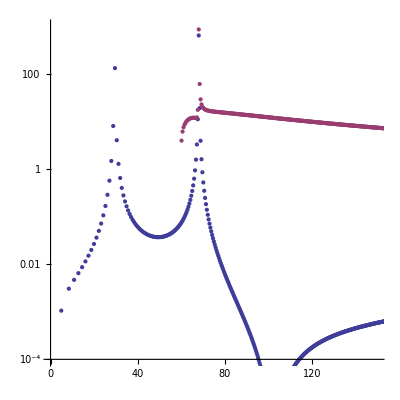

```mathematica
ListLogPlot[
	,
AspectRatio->1,PlotRange->{{0,150},{1*^-4,1*^3}}]
```

```mathematica
vv
```

```mathematica
(* Cross sections as fucntion of sneutrino mass *)
ListPointPlot3D[
{Transpose@{f results[[;;pass,2,3,8]],results[[;;pass,1,3,4]],Log[10,results[[;;pass,4,1]]]},
Transpose@{f results[[;;pass,2,3,8]],results[[;;pass,1,3,4]],Log[10,results[[;;pass,4,2]]]}}]
```

```mathematica
Export["fig7-lambdaN-0004.eps",%567]
```

fig7-lambdaN0045.eps

```mathematica
Save["/Users/ruppell/Math/Santosh/dataFig6lamN",results];
```

In the part below I try to plot some analytic results instead of doing the loop. This is possible since the mixing matrix doesn’t actually change at all for the range of MNR that Cerdeno is scanning and only the mass eigenvalues change. Thus it is possible to take the lightest sneutrino mass as a variable and express the mandelstam s with it and plot cross sections.

```mathematica
Clear@s
```

```mathematica
lambdaN=0.004`50;
dNNH=Outer[D[Vsc,##]&,fieldsSneutrino,fieldsSneutrino,fieldsScalarN]/.allVEV/.{phiS->0,phi2->0};
dHHH=Outer[D[Vsc,##]&,fieldsScalarN,fieldsScalarN,fieldsScalarN]/.allVEV/.{phiS->0,phi2->0};
dNNHH=Outer[D[Vsc,##]&,fieldsSneutrino,fieldsSneutrino,fieldsScalarN,fieldsScalarN]/.allVEV/.{phiS->0,phi2->0};
dFFH=Outer[D[Vv,##]&,fieldsBquark,fieldsBquarkC,fieldsScalarN]/.allVEV/.{phiS->0,phi2->0};
```

```mathematica
func=Mbb/.s->(2 (x+1) GeV)^2/.(1-Cos[θ])->4Pi;
func2=Sqrt[s/4-mbottom^2]/Sqrt[s/4-(x GeV)^2]/(64 Pi^2 s) func 0.389*^27/.s->(2 (x+1) GeV)^2;
```

```mathematica
func3=Mhh[5]/.s->(2 (x+1) GeV)^2;
func4:=NIntegrate[Sin[θ]func3,{θ,0,Pi},{ϕ,0,2Pi},AccuracyGoal->16]
func5=Sqrt[s/4-mH[[5]]^2]/Sqrt[s/4-(x GeV)^2]/(64 Pi^2 s)  0.389*^27/.s->(2 (x+1) GeV)^2;
```

```mathematica
Off@NIntegrate::ncvb;
```

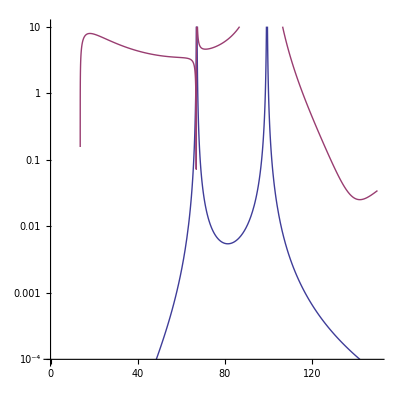

```mathematica
LogPlot[{func2,func4 func5},{x,0,150},
AspectRatio->1,
PlotRange->{{0,150},{1*^-4,1*^1}},PlotPoints->200]
```

```mathematica
Export["plot7-lambdaN-0004.eps",%525]
```

plot7-lambdaN-0004.eps

```mathematica
-0.01,-0.008,-0.006,-0.005,-0.004
```

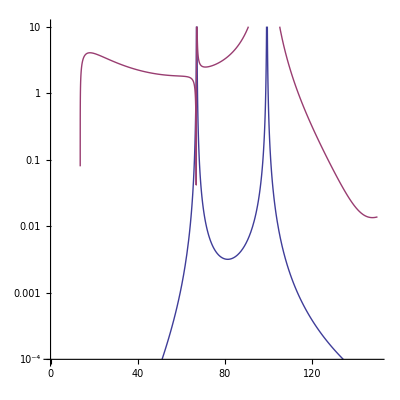
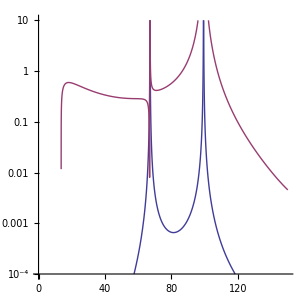
```mathematica
plotsNeg={-Graphics-,-Graphics-,-Graphics-,-Graphics-};
```

```mathematica
0.0001,0.001,0.003,0.004,0.005,0.006,0.01,0.012,0.013,0.014,0.015,0.02
```

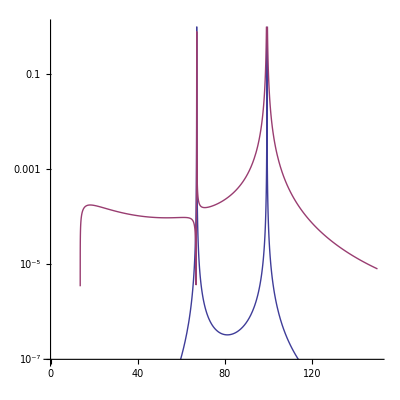
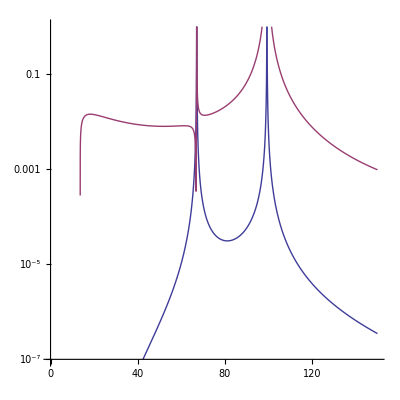
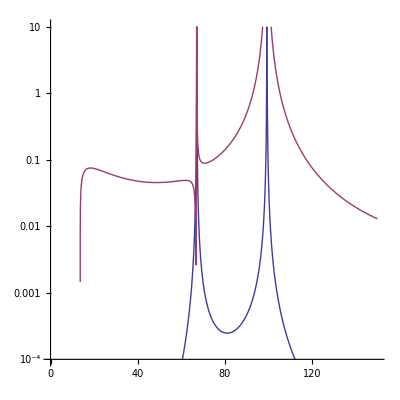
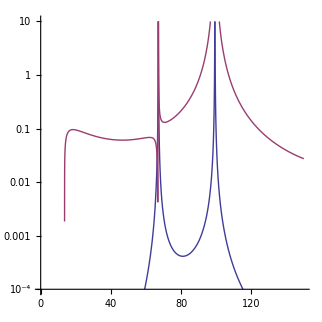
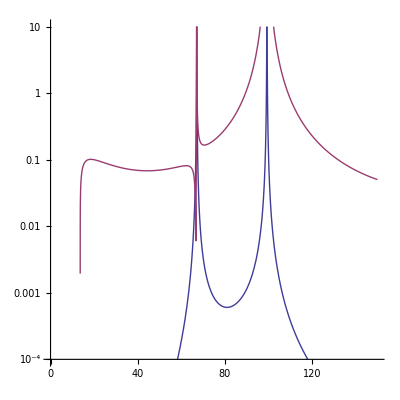
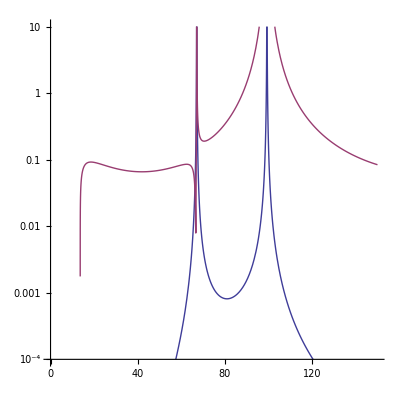
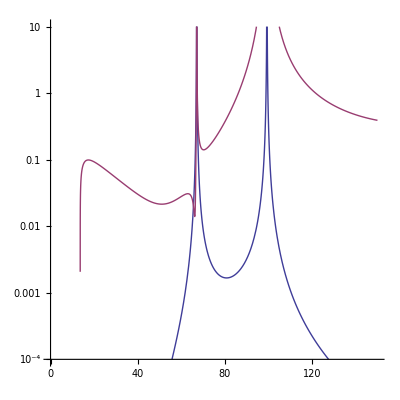
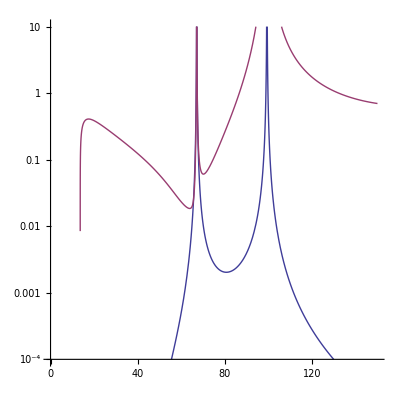
```mathematica
plots1={-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-};
```

```mathematica
0.04,0.045,0.05,0.055,0.06,0.07,0.08,0.09,0.1,0.2,0.3,0.4
```

```mathematica
plots2={-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-};
```

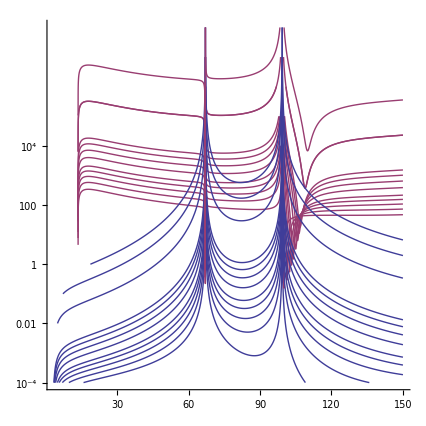

```mathematica
Show[plots2,PlotRange->Automatic]
```

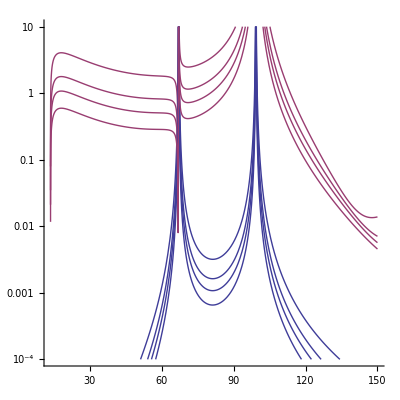

```mathematica
Show[plotsNeg,PlotRange->Automatic]
```